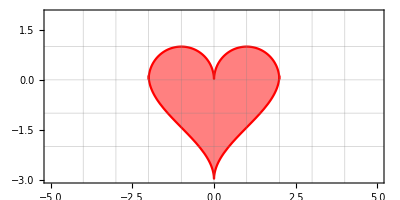

```mathematica
f[x_]:=√(1-(Abs[x]-1)^2)
g[x_]:=ArcCos[1-Abs[x]]-3
Plot[{f[x],g[x]},{x,-3,3},PlotRange->{{-5,5},{-3,2}},Frame->True,GridLines->{Range[-4,4],Range[-2,1]},AspectRatio->0.5,Filling->{1->{{2},Pink}},PlotStyle->Red]
```

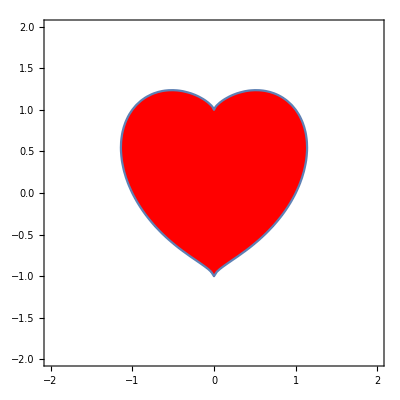

```mathematica
RegionPlot[(x^2+y^2-1)^3-x^2 y^3≤0,{x,-2,2},{y,-2,2},PlotStyle->Red]
```

```mathematica
ContourPlot3D[(2 x^2+y^2+z^2-1)^3-(x^2 z^3)/10-y^2 z^3==0,{x,-1.3,1.3},{y,-1.3,1.3},{z,-1.3,1.3},MeshFunctions->{#3&,#2&},Mesh->50,Axes->False,Boxed->False,MeshShading->{{FaceForm[Cyan,None],FaceForm[None,Cyan]},{FaceForm[None,Cyan],FaceForm[Cyan,None]}}]
```

-Graphics3D-